# Mathematica Notes - Basins of Attraction

## Introduction

An attractor of a dynamical system is a subset of the phase space of a dynamical system towards which the long-time behaviour of typical initial conditions tend towards. A typical example is given by the following forced damped pendulum equation [1]:

```mathematica
FDPE= θ''[t] + 1/10 θ'[t] + Sin[θ[t]] == 21/10 Cos[t]
```

Sin[θ[t]]+θ'[t]/10+θ''[t]==(21 Cos[t])/10

In the example given, there are two attracting states, both of which are periodic orbits.

```mathematica
Manipulate[Plot[θ[time]/.First@NDSolve[{FDPE,θ[0]==θ0,θ'[0]==ω0},θ,{t,0,200}],{time,150,200},AxesLabel->{"t","θ[t]"},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}],{θ0,-π,π},{ω0,-5,5}]
```

## Calculating basins of attraction

To calculate the whether or not a solution starting from some initial condition ends up at which basin of attraction, we must first devise a test. Rigorously, one would like to calculate first the period of the attractors, and use this as a stringent test: |(θ[t] mod 2π) - (θ[t+T] mod 2π)| < δ

Less careful would be to use the fact that each attractor either runs away to positive infinite θ or to negative infinite θ. Thus, a less careful test would be to stop integration when |θ[t]| > θ_max, and simply check whether the θ[t] is positive or negative corresponding to the two attractors.

For this, we use the Catch and Throw commands of Mathematica, and assign a value of 0 for initial conditions that run off to positive infinity, and 1 for initial conditions that run off to negative infinity. We also use the WhenEvent subfunction of NDSolve, to check whether it has reached either attractor, or we have calculated above our maximum simulation time (which we assign a value of 2)

```mathematica
CheckAttractor[θ0_,ω0_,MaximumT_,Maximumθ_]:=Catch[NDSolve[{FDPE,θ[0]==θ0,θ'[0]==ω0,WhenEvent[θ[t]>Maximumθ,Throw[0]],WhenEvent[θ[t]<-Maximumθ,Throw[1]],WhenEvent[t>MaximumT,Throw[2]]},θ,{t,0,MaximumT+1}]]
```

Eventually, we are going to color these states using the ColorRules option of MatrixPlot. We save these rules under the following variable.

```mathematica
AttractorColors = {0->White,1->Black,2-> Red};
```

We also define our maximum simulation time, our θ cutoff and the number of pixels of our basin plot

```mathematica
MaximumT = 1000; Maximumθ=300;pixels=200;
```

We now calculate the basin of attraction

```mathematica
Basins = Table[CheckAttractor[θ0,ω0,MaximumT,Maximumθ],{ω0,Subdivide[-5,5,pixels]},{θ0,Subdivide[-π,π,pixels]}];//Timing
```

{1358.25,Null}

Plotting the basins of attraction, we get

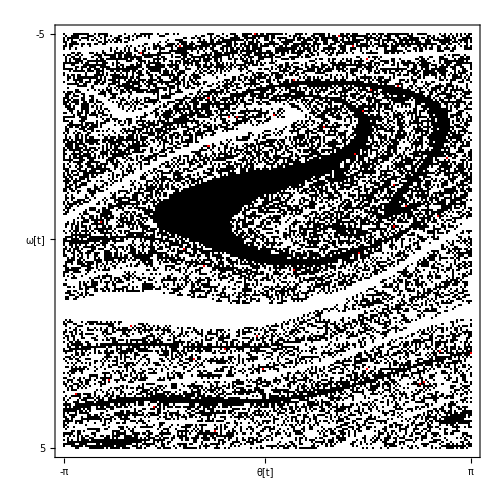

```mathematica
MatrixPlot[Basins,ColorRules->AttractorColors,FrameTicks->{{{1,-5},{pixels/2,"ω[t]"},{pixels+1,5}},{{1,-π},{pixels/2,"θ[t]"},{pixels+1,π}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## ParallelTable

Now it seems like an awful lot of bother to calculate a 200x200 pixel image for 22 minutes. One might also observe that, on a single kernel, we are using only a fraction of the computational strength of our computer. In my laptop, each run uses around only ~30% of the CPU. We may speed this calculation up, since calculating the basin of a pixel is independent of other pixels. Thus, we may parallelize the computation of the basin.

This can be readily done using an built-in Mathematica function: ParallelTable. First let us check how many kernels are there:

```mathematica
$KernelCount
```

0

We may launch several kernels locally using the LaunchKernel command

```mathematica
LaunchKernels[3]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local]}

The relevant command would just be to replace Table with ParallelTable. In my computer, the following command now uses ~90% of the CPU.

```mathematica
Basins = ParallelTable[CheckAttractor[θ0,ω0,MaximumT,Maximumθ],{ω0,Subdivide[-5,5,pixels]},{θ0,Subdivide[-π,π,pixels]}];//AbsoluteTiming
```

{575.906,Null}

We get the same output for a fraction of the time. Of course the savings are linear, as opposed to the quadratic scaling of the problem at hand.

```mathematica
MatrixPlot[Basins,ColorRules->AttractorColors,FrameTicks->{{{1,-5},{pixels/2,"ω[t]"},{pixels+1,5}},{{1,-π},{pixels/2,"θ[t]"},{pixels+1,π}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

-Graphics-

## References

[1] Grebogi, C., Ott, E.and Yorke, J.A.(1987) Basin Boundary Metamorphoses : Changes in Accessible Boundary Orbits, Physica D 24 : 243.